# Bloque 2 - Manipulaciones simbólicas

### Autor: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

## Operaciones algebraicas y cálculo

Álgebra

El lenguaje WL facilita la manipulación de elementos simbólicos. Debido a esto se pueden establecer elementos que no necesitan ser evaluados, facilitando así la posibilidad de realizar operaciones algebraicas. Es por ejemplo totalmente válido hacer

```mathematica
FullForm[(x+√y)^2]
```

Power[Plus[x,Power[y,Rational[1,2]]],2]

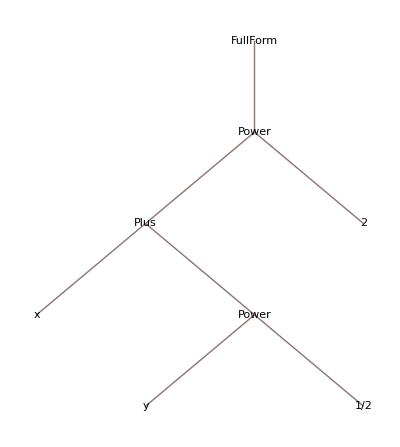

```mathematica
TreeForm[FullForm[(x+√y)^2]]
```

Y realizar una operación sobre este elemento simbólico

```mathematica
Expand[(x+√y)^2]
```

x^2+2 x √y+y

Por último, la evaluación se puede realizar a través de reglas:

```mathematica
Expand[(x+√y)^2] /.{x->3,y-> 8}
```

17+12 √2

```mathematica
N[17+12 √2]
```

33.9706

O asignando valores a las variables

```mathematica
With[{x=3,y=8},(x+√y)^2]
```

(3+2 √2)^2

```mathematica
N[(3+2 √2)^2]
```

33.9706

Nótese que Mathematica deja la expresión en forma simbólica, no la evalúa.

```mathematica
FullForm[17+12 √2]
```

Plus[17,Times[12,Power[2,Rational[1,2]]]]

Para forzarlo a que realice la evaluación se utiliza la función N[] que transforma la forma numérica a una expresión a atómica del tipo Real.

```mathematica
N[17+12 √2]
```

33.9706

Podemos especificarle el número de decimales que queremos

```mathematica
N[π,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

En Mathematica hay muchas funciones numéricas predefinidas, como Sin, Cos, Tan, Log, etc...

```mathematica
Sin[5]
```

Sin[5]

```mathematica
Sin[π/2]
```

1

```mathematica
x = N[Sin[5]]
```

-0.958924

Se pueden manipular expresiones algebraicas.
Para simplificar

```mathematica
Clear[x]
```

```mathematica
expresion = (x^2+1)x+6x
```

6 x+x (1+x^2)

```mathematica
FullSimplify[expresion]
```

x (7+x^2)

Para expandir

```mathematica
Expand[expresion]
```

7 x+x^3

Hay funciones para factorizar donde se puede especificar el factor

```mathematica
FactorTerms[3x y^2+6y x+3y x^2+3 x^2 y^4,x]
```

3 y (2 x+x^2+x y+x^2 y^3)

```mathematica
FactorTerms[3x y^2+6y x+3y x^2+3 x^2 y^4,y]
```

3 x (2 y+x y+y^2+x y^4)

También se pueden resolver ecuaciones algebraicas. Solve[] las resuelve de manera simbólica.

```mathematica
Solve[x== 7x+9,x]
```

{{x→-3/2}}

```mathematica
x /.Solve[x== 7x+9,x]
```

```mathematica
Solve[Sin[x]==0.8,x]
```

{{x→0.927295}}

Algunas veces la manera simbólica de resolver ecuaciones no es la más eficiente,

```mathematica
Solve[Cos[x]==x,x,Reals]
```

{{x→Root0.739Root[{-Cos[#1]+#1&,0.73908513321516064166}]0.7390851332151607}}

es por eso que existe la opción de resolver la ecuación numéricamente.

```mathematica
NSolve[Cos[x]==x,x,Reals]
```

{{x→0.739085}}

Para resolver ecuaciones simultáneas se hace

```mathematica
Solve[{x+y==7,4x-5y == 2},{x,y}]
```

{{x→37/9,y→26/9}}

### Ejercicio 1:

Resolver la ecuación cuadrática a x^2+b x+c==0, luego resolver la ecuación cúbica a x^3+b x^2+c x + d0

```mathematica
Solve[a x^4+b x^3+c x^2 + d x + e == 0,x]
```

### Ejercicio 2:

Resolver el sistema de ecuaciones
Cos(x+y) = x,
y = x+2

Cálculo

Mathematica puede hacer operaciones de cálculo de manera simbólica, por ejemplo derivadas

```mathematica
D[x^7,x]
```

7 x^6

```mathematica
D[Log[Sin[Exp[x]]^2],x]
```

2 ⅇ^x Cot[ⅇ^x]

Para evaluar la derivada en algún punto se puede usar una regla de sustitución

```mathematica
D[Log[Sin[Exp[x]]^2],x]
```

2 ⅇ^x Cot[ⅇ^x]

```mathematica
N[D[Log[Sin[Exp[x]]^2],x] /. {x->8}]
```

-13589.1

De manera análoga se pueden realizar integrales

```mathematica
Integrate[7 x^6,x]
```

x^7

```mathematica
Integrate[Log[Sin[Exp[x]]^2],x]
```

∫Log[Sin[ⅇ^x]^2]ⅆx

Se puede evaluar la integral en un intervalo. Por defecto Mathematica trata de hacerlo de manera simbólica

```mathematica
Integrate[7 x^6,{x,5,6}]
```

201811

Sin embargo no siempre tiene éxito.

```mathematica
Integrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

∫_0.5^1 Log[Sin[ⅇ^x]^2]ⅆx

En éstos casos es necesario realizar la integral numéricamente.

```mathematica
NIntegrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

-0.244913

### Ejercicios

#### Ejercicio 1:

Verificar si se cumple el teorema fundamental del cálculo en las funciones de Mathematica.

```mathematica
Integrate[D[f[x],x],x]
```

f[x]

#### Ejercicio 2:

Encontrar la solución numérica a la ecuación

∫√(x+√x)dx= x donde x ∈ Reales

```mathematica
Integrate[√(x+√x),x]
```

1/12 √(√x+x) (-3+2 √x+8 x+(3 ArcSinh[x^(1/4)])/(√(1+√x) x^(1/4)))

```mathematica
NSolve[Integrate[√(x+√x),x] ==x,x,Reals]
```

{{x→0.881431}}

#### Ejercicio 4:

Sea f(x) una función de la cual se desea conocer sus raíces, y sea x_0 un punto inicial. Se desea encontrar un x_0+ϵ tal que se acerque a la raíz.
Expandiendo se tiene que

f(x_0+ϵ) = f(x_0) + ϵ f'(x_0) + 1/2 ϵ^2 f''(x_0) + ...

Aproximando para valores muy pequeños de ϵ se obtiene que

f(x_0+ϵ) ≃ f(x_0) + ϵ f'(x_0)

Si x_0+ϵ es un punto cercano a la raíz entonces se tiene que cumplir que

f(x_0+ϵ) ≃ 0

entonces queda que

ϵ = - (f(x_0))/(f'(x_0))

A partir de esto se puede construir un método iterativo para aproximarnos a la raíz,

x_1 = x_0 + ϵ = x_0 - (f(x_0))/(f'(x_0)).

Este es el método de Newton-Rhapson, definido por

x_(n+1) = x_n -(f(x_n))/(f'(x_n)).

El ejercicio es el siguiente:

Implementar el método de Newton-Rhapson para una ecuación arbitraria

```mathematica
f[x_]:=x^3-1;
```

```mathematica
NewtonRhapson[f,0.5,10]
```

### Proyecto

El exponente de Lyapunov, λ, es un parámetro que cuantifica qué tanto divergen dos órbitas infinitesimalmente cercanas.

-Graphics-
-Graphics-

El ejercicio consiste en implementar un cálculo del exponente de Lyapunov para el mapeo logístico.

#### Solución

Órbita del mapeo logístico

```mathematica
LogisticEquation[r_,x_]:=r x (1-x);
LogisticMap[r_,x0_,iter_]:=Drop[NestList[LogisticEquation[r,#]&,x0,iter+100],100];
LogisticR[rmin_,rmax_,dr_]:=Flatten[Table[Thread[{r,LogisticMap[r,0.22,300]}],{r,rmin,rmax,dr}],1];
```

Gráfica del mapeo logístico

```mathematica
ListPlot[LogisticR[2,4,0.005]]
```

Cálculo de Lyapunov

```mathematica
LogisticPrime[r_,x_]=D[LogisticEquation[r,x],x];
```

```mathematica
Lyapunov[r_,x0_,iter_]:=Block[{logs,sum},
logs = Map[Log[Abs[LogisticPrime[r,#]]]&,LogisticMap[r,x0,iter]];
sum =Total[Drop[logs,1]];
Return[sum/Length[logs]];
];
```

```mathematica
Plot[Lyapunov[r,0.25,100],{r,2,4}]
```

Vistas juntas

```mathematica
Column[
{
ListPlot[
LogisticR[2,4,0.005],
PlotTheme->"Scientific",
FrameLabel->{"r","x"},
PlotLabel->"Órbita",
ImageSize->400
],
Plot[
Lyapunov[r,0.25,100],
{r,2,4},
PlotTheme->"Scientific",
FrameLabel->{"r","λ"},
PlotLabel->"Lyapunov",
ImageSize->400
]
}
]
```

## Introducción a las gráficas

Introducción

WL es un lenguaje de naturaleza simbólica, eso significa que no hace distinción entre un tipo de datos numérico como un entero, y un gráfico. La capacidad de mezclar elementos de cualquier tipo es una de sus características más poderosas ya que resulta relativamente fácil implementar gráficos con elementos interactivos, valores numéricos y todo tipo de funcionalidades.

La función gráfica más elemental es Graphics[], de la cual se derivan todos los demás elementos gráficos. Graphics trabaja con elementos simples denominados primitivas, por ejemplo:

```mathematica
Graphics[Line[{{1,0},{2,1},{3,0},{4,1}}]]
```

Es posible combinar varias primitivas:

```mathematica
Graphics[{Disk[],Line[{{1,0},{2,1},{3,0},{4,1}}]}]
```

Y establecer directivas para cada una de las primitivas:

```mathematica
Graphics[{Blue,Disk[],Red,Thick,Line[{{1,0},{2,1},{3,0},{4,1}}]}]
```

Gráficas de funciones

Para efectos práctivos uno no suele utilizar las primitivas básicas ya que existen funciones que crean elementos gráficos de forma adecuada para graficar funciones. La gráfica más simple se puede crear con una función Plot, que grafica funciones definidas en los números reales.

```mathematica
Plot[Sin[x],{x,0,6π}]
```

Para aumentar la cantidad de detalles que se muestra en la gráfica se pueden utilizar argumentos opcionales

```mathematica
Plot[Sin[x],{x,0,6π},PlotTheme->"Scientific",FrameLabel->{"Eje x","Eje y"},GridLines->Automatic]
```

Algunas funciones discontinuas no se pueden graficar adecuadamente con Plot, para esto está DiscretePlot

```mathematica
Row[{Plot[MoebiusMu[k],{k,1,50},ImageSize->400],DiscretePlot[MoebiusMu[k],{k,1,50},ImageSize->400]}]
```

Se pueden agrupar varias gráficas

```mathematica
Plot[{x^2,Sin[x]},{x,0,3},PlotTheme->"Scientific", FrameLabel->{"x","f(x)"},ImageSize->400,BaseStyle->FontSize->16,GridLines->Automatic,Filling->Bottom,PlotLegends->{"x^2","Sen(x)"}]
```

Combinar gráficas a veces es útil para crear efectos

```mathematica
Show[
Plot[Log[Sin[Exp[x]]^2],{x,0.5,1},PlotTheme->"Scientific"],
Plot[Log[Sin[Exp[x]]^2],{x,0.5,0.8},Filling->Top,PlotTheme->"Scientific"]
]
```

Existen más tipos de gráficas que se pueden realizar, como gráficas en 3d

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotTheme->"Scientific", AxesLabel->{"x","y","z"},BaseStyle->FontSize->16]
```

Se pueden realizar gráficas implícitas. Nótese que la intersección coincide con la solución.

```mathematica
N[Solve[{x+y==7,4x-5y == 2},{x,y}]]
ContourPlot[{x+y==7,4x-5y == 2},{x,-5,5},{y,-5,5}]
```

#### Ejercicio 1:

Graficar

Cos(x+y) = x,
y = x+2

y comprobar que la intersección coincide con la solución del sistema de ecuaciones.

Elementos interactivos

```mathematica
Manipulate[i^2,{i,0,10}]
```

```mathematica
Manipulate[
Plot[{x^2,Sin[a x]},
{x,0,3},
PlotTheme->"Scientific",
 FrameLabel->{"x","f(x)"},
ImageSize->400,
BaseStyle->FontSize->16,
GridLines->Automatic,
Filling->Bottom,
PlotLegends->{"x^2","Sen(ax)"}
],
{a,1,5}
]
```

#### Ejercicio

Crear un elemento interactivo que encuentre la solución de
Cos(x+y) = ax,
y = x+2,
donde a es un elemento variable de 1 a 2.

Elementos dinámicos

```mathematica
Row[{InputField[Dynamic[x]],Dynamic[StringLength[ToString[x]]]}," "]
```

### Proyecto: El péndulo simple como mapeo

Un método numérico sencillo (y propenso a errores) de resolver una ecuación diferencial es el método de Euler, que consiste en dada una ecuación diferencial

(d y(t))/dt=f(t,y(t))

aproximarla tomando intervalos finitos

(d y(t))/dt≃ Δy/Δt= (y_(n+1 - y_n))/Δt=f(t,y(t)) ,

de manera que

y_(n+1) = y_n + Δt f(t,y(t))

Esto en esencia es un mapeo. Podemos hacer uso de este método para resolver una ecuación diferencial de un sistema físico como el péndulo simple, cuya dinámica está descrita por

θ^(..)+ g/l Sin(θ) = 0

-Graphics-

El objetivo del proyecto consiste en resolver la ecuación diferencial y graficar el péndulo en movimiento.
Parte 1: Dados los parámetros

```mathematica
g = 9.81; l= 1; Δt = 0.05;
```

Y las funciones de evolución

```mathematica
Velocidad[v_,x_]:=v - (g Sin[x])/l Δt;
Posicion[v_,x_]:=x + v Δt;
```

calcular la dinámica del péndulo utilizando el método de Euler.

Parte 2: Una vez que se tienen todos los puntos que describen la dinámica en θ, si queremos visualizarlos en el plano cartesiano es necesario convertirlos a puntos {x,y}.

Parte 3: Crear una función llamada VisualizacionPendulo[{x,y}] que cree una visualización del péndulo

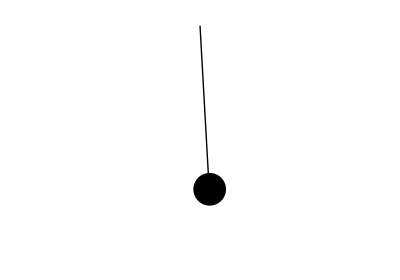

Parte 4: Mapear la función VisualizacionPendulo a los puntos {x,y} de la dinámica y animar con Manipulate o ListAnimate.

#### Solución:

```mathematica
g=9.81;l=1;dt=0.05;
Velocidad[v_,x_]:=v-(g Sin[x])/l dt;
Posicion[v_,x_]:=x+v dt;

espacioFase=NestList[{Velocidad[First[#],Posicion[First[#],Last[#]]],Posicion[First[#],Last[#]]}&,{0,0.7},100];

theta=espacioFase[[All,2]];
xy=Map[{Sin[#],-Cos[#]}&,theta];
DiagramaPendulo[{x_,y_}]:=Block[{linea,disco,diagrama},linea=Line[{{0,0},{x,y}}];
disco=Disk[{x,y},0.1];
diagrama=Graphics[{linea,disco},PlotRange->{{-1,1},{-1.2,0.5}}];
Return[diagrama];];

cuadros=Map[DiagramaPendulo,xy];
Manipulate[cuadros[[i]],{i,1,Length[cuadros],1}]
```

## Problema de repaso: Algoritmo de compresión de audio

Comencemos con una pregunta simple, si dos instrumentos musicales diferentes, como por ejemplo un piano y una guitarra, están tocando la misma nota, ¿Qué es lo que diferencia el timbre de ambos?

#### Cargar el archivo de audio

Para responder la pregunta se puede analizar un archivo de audio utilizando el lenguaje Wolfram con el fin de entender cuáles son las características de cada sonido.

Primero se carga el archivo de audio.

```mathematica
audio = Import[FileNameJoin[{NotebookDirectory[],"audio.aiff"}]];
```

En el lenguaje Wolfram el audio se queda guardado en una variable, a la cual se puede acceder para escucharlo.

```mathematica
audio
```

Las señales de audio que registran todos los dispositivos electrónicos de grabación son en realidad un conjunto de puntos que representan una onda. Estos puntos son grabados a una frecuencia de muestreo específica. La frecuencia de muestreo es la cantidad de puntos de la onda de audio que se registran en cada segundo. Por lo general la mayoría de los dispositivos de audio graba o reproduce con una frecuencia de muestreo de 44100 Hz.

Para averiguar la frecuencia de muestreo de nuestro audio primero debemos obtener los puntos que conforman nuestra señal.

```mathematica
data = First[AudioData[audio]];
```

Luego se averigua la duración. El lenguaje Wolfram nos devuelve la duración en la unidad de segundos.

```mathematica
duracion = Duration[audio]
```

Por último la frecuencia de muestreo es la cantidad de muestras dividida por la duración total de la señal.

```mathematica
AudioSampleRate[audio]
```

```mathematica
samplerate = QuantityMagnitude[Quantity[AudioSampleRate[audio],"Hertz"]]
```

#### Visualización de señal

Para visualizar la señal de audio en su totalidad se puede usar la función AudioPlot que se encuentra definida en el lenguaje Wolfram. El problema es que con esta función no se puede apreciar todavía el caracter ondulatorio de la señal.

```mathematica
AudioPlot[audio, FrameLabel->{"Tiempo [s]", "Amplitud"}]
```

Para poder visualizar las ondas es necesario realizar una ampliación. Para esto podemos partir de la lista de las muestras. Primero se hace una sublista en un intervalo pequeño, por ejemplo, desde la muestra 100000 a la muestra 102000, es decir, tomamos 2000 muestras desde el tiempo 2.26757 [s] hasta el tiempo 2.31293 [s].

```mathematica
sublista = Take[data,{100000,102000}];
```

Y se grafica la sublista.

```mathematica
ListLinePlot[sublista, PlotTheme->"Scientific", FrameLabel->{"Indice", "Amplitud"}]
```

Se puede observar que el sonido que produce una guitarra también es una onda que oscila a una frecuencia determinada, pero tiene una forma muy compleja que es producto de la suma de muchas frecuencias. ¿Cómo podemos saber las frecuencias que componen una onda?

#### Visualización de las frecuencias que componen una señal de audio

Transformada de Fourier para una muestra

La Transformada De Fourier es una herramienta matemática que nos permite encontrar cuáles son las frecuencias que componen una señal. Existen numerosas variaciones del concepto, nosotros nos centraremos en la Transformada Discreta De Fourier que se puede aplicar a señales discretas, esto es que se muestrean en intervalos de tiempo regulares como en el caso del audio. La implementación que nos conviene usar para la transformada de Fourier se encuentra en el lenguaje Wolfram en la función FourierDCT.

Para usarla primero se parte la señal de audio en varios pedazos, los cuales tienen un tamaño proporcional a medio segundo.

```mathematica
samples = Partition[data, samplerate/2];
```

```mathematica
ListPlay[samples[[6]],SampleRate->samplerate]
```

Nos fijamos que la sección de audio que mejor suena para realizar el análisis es la sexta, así que se realiza la transformada de Fourier en la sexta muestra.

```mathematica
transformada =  FourierDCT[samples[[6]]];
```

Por último, para obtener la intensidad de las frecuencias se toma el valor absoluto de la transformada de Fourier.

```mathematica
transformadaabsoluta = Abs[transformada];
```

Y se grafica

```mathematica
ListLogPlot[transformadaabsoluta[[1;;2000]],PlotRange->Full, PlotTheme->"Scientific", FrameLabel->{"Frecuencia", "Intensidad"}]
```

### Ejercicio:

Identificar la frecuencia fundamental (la que tiene mayor intensidad) y crear una señal similar usando Play[]. Comparar con el audio de la grabación. ¿Es la misma nota?

#### Solución:

Resultado:

```mathematica
Play[Sin[109 2Pi t],{t,0,1},SampleRate->samplerate]
```

#### Búsqueda de frecuencias fundamentales y reconstrucción de la señal

¿Cuáles son las frecuencias fundamentales? Se puede hacer uso de la función FindPeaks para encontrar las frecuencias fundamentales junto con su amplitud.

```mathematica
submuestra = Take[transformadaabsoluta,4000];
picos = FindPeaks[submuestra,10];
ListLogPlot[submuestra, Epilog-> {Red,PointSize[0.01],Point[picos]}, PlotTheme->"Scientific", FrameLabel->{"Frecuencia", "Intensidad"}]
```

Con esto podemos conocer cuáles son las magnitudes de las frecuencias

```mathematica
freq = picos[[All,1]]
```

Y sus amplitudes

```mathematica
amplitud = picos[[All,2]]
```

Con esta información además se puede reconstruir una señal que es parecida a la señal original

```mathematica
Play[Sum[amplitud[[i]] Sin[freq[[i]] 2Pi t],{i,1,Length[picos]}],{t,0,2}]
```

Y al compararla con la señal original se observa que son muy parecidas.

```mathematica
ListPlay[samples[[6]],SampleRate->samplerate]
```

Es notable el contraste entre la cantidad de información que se necesita para almacenar ambas señales. Para almacenar la señal original se requieren almacenar 22050 números.

```mathematica
Length[samples[[6]]]
```

Mientras que para almacenar la señal que se obtiene de los picos se requieren almacenar 110 números

```mathematica
Length[Flatten[picos]]
```

¡Esto es se comprimió la señal al 0.49 % de su tamaño! Este es un ejemplo de cómo funciona el principio sobre el cual se rigen los algoritmos de compresión de audio como el mp3 o mp4, los cuales utilizan practicamente todos los dispositivos modernos.

```mathematica
100*N[Length[Flatten[picos]]/Length[samples[[6]]]]
```

#### Ejercicio:

Verificar cómo varía la reconstrucción de la señal usando n picos de la transformada de Fourier. Crear una tabla de reconstrucciones con n que vaya desde 1 hasta 30.

### Transformada de Fourier para todo el audio

Si se desea obtener la transformada de Fourier utilizando el archivo de audio en su totalidad se puede usar la función Periodogram que está incluida en el lenguaje Wolfram.

Por defecto Periodogram dibuja la gráfica en la escala logarítmica.

```mathematica
Periodogram[audio,AxesLabel->{"Frecuencia", "Amplitud (dB)"}]
```

Si nos interesa estudiar las frecuencias más bajas [0,500] se puede limitar la gráfica a ese intervalo.

```mathematica
Periodogram[audio,PlotRange->{{0,500},Full},AxesLabel->{"Frecuencia", "Amplitud (dB)"}]
```

En caso de que no se desee utilizar utilizando el escalamiento logarítmico ésto se puede especificar en la función de escalamiento.

```mathematica
Periodogram[audio,ScalingFunctions->"Absolute",PlotRange->{{0,500},Full},AxesLabel->{"Frecuencia", "Amplitud"}]
```

Algoritmo de compresión de audio

### Compresión

Primero se carga el audio y se guardan cuáles son sus parámetros.

```mathematica
compressioncut = 30000;
```

```mathematica
samplesize = samplerate
```

Se parte la muestra en varios segmentos

```mathematica
samples = Partition[data, samplesize];
```

A cada uno de los segmentos se le calcula la transformada de Fourier, la cual nos da la amplitud de las frecuencias que componen la señal.

```mathematica
fouriersamples = ParallelTable[FourierDCT[i],{i,samples}];
```

Y por último se cortan las frecuencias más altas

```mathematica
fouriersamplescut = fouriersamples[[All,1;;(samplesize-compressioncut)]];
```

Se aplana la lista para obtener una lista de datos tal como se encontraría en una archivo comprimido.

```mathematica
compressedaudio = Flatten[fouriersamplescut];
```

Podemos averiguar la tasa de compresión.

```mathematica
N[Length[compressedaudio]/Length[data]]
```

### Descompresión

Para descomprimir la señal  se particiona la muestra comprimida

```mathematica
compressedsamples = Partition[compressedaudio, samplesize-compressioncut];
```

Y se reconstruye la muestra utilizando de nuevo la transformada de Fourier y rellenando los espacios recortados con ceros.

```mathematica
reconstructedsamples =  ParallelTable[FourierDCT[Join[i,ConstantArray[0,compressioncut]]],{i,compressedsamples}];
restoredaudio = Flatten[reconstructedsamples];
```

El audio reconstruido se puede reproducir con ListPlay. Es notable la pérdida de calidad y el chasqueo.

```mathematica
ListPlay[restoredaudio, SampleRate->samplerate]
```

La pérdida de calidad también se puede apreciar en el periodograma

```mathematica
Periodogram[audio, AxesLabel->{"Frecuencia", "Amplitud"},PlotLabel->"Señal original"]
```

```mathematica
Periodogram[restoredaudio,SampleRate->samplerate, AxesLabel->{"Frecuencia", "Amplitud"},PlotLabel->"Señal reconstruida"]
```

#### Ejercicio:

Crear un algoritmo de compresión que elimine las frecuencias más bajas en vez de las frecuencias altas. ¿Cómo se escucha el resultado?

## Ecuaciones diferenciales

Anteriormente hemos resuelto la ecuación diferencial que describe al péndulo simple utilizando el método de Euler como un mapeo. En la realidad no es práctico hacer eso cada vez que nos enfrentamos a ese problema. Mathematica ya tiene integradas rutinas que permiten resolver ecuaciones diferenciales tanto de forma analítica como numérica. ¿Cuál conviene utilizar? Depende de cada caso, veamos un ejemplo.

Caso de ejemplo: Péndulo simple

Regresemos de nuevo al ejemplo del péndulo simple descrito por la ecuación diferencial

θ^(..)(t)+ g/l Sin(θ(t)) = 0

-Graphics-

Para trabajar este sistema es común realizar una aproximación para ángulos pequeños, argumentando que θ ≃ Sin(θ) se suele reescribir como

θ^(..)(t)+ g/l θ(t) = 0.

La ventaja de expresarlo de esta manera es que la ecuación posee soluciones analíticas, las cuales en Mathematica podemos obtener utilizando DSolve.

```mathematica
DSolve[θ''[t]+g/l θ[t]==0,θ,t]
```

{{θ→Function[{t},C[1] Cos[(√g t)/(√l)]+C[2] Sin[(√g t)/(√l)]]}}

DSolve siempre nos devuelve la forma más general de una solución, incluyendo constantes arbitrarias denotadas por C[n]. Estas pueden ser  eliminadas introduciendo constricciones al sistema de ecuaciones diferenciales.

```mathematica
DSolve[{θ''[t]+g/l θ[t]==0,θ[0]==1,θ'[0]==0},θ,t]
```

{{θ→Function[{t},Cos[(√g t)/(√l)]]}}

Una vez resuelta la ecuación diferencial, ¿cómo se grafica? La solución viene expresada como una regla de sustitución, de manera que aplican las mismas reglas que cuando resolvimos ecuaciones algebraicas.

{{θ→Function[{t},1. Cos[3.1305 t]]}}

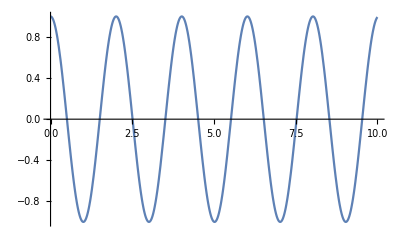

```mathematica
solucion = With[{g=9.8,l=1},DSolve[{θ''[t]+g/l θ[t]==0,θ[0]==1,θ'[0]==0},θ,t]]
Plot[θ[t]/.First[solucion],{t,0,10}]
```

Si intentamos hacer lo mismo con la ecuación diferencial sin la aproximación DSolve devuelve errores. La causa de esto es que no existe una solución analítica.

```mathematica
DSolve[{θ''[t]+g/l Sin[θ[t]]==0,θ[0]==1,θ'[0]==0},θ,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

En estos casos conviene resolver la ecuación numéricamente

```mathematica
completa = With[{g=9.8,l = 1},NDSolve[{θ''[t]+g/l Sin[θ[t]]==0,θ[0]==1,θ'[0]==0},θ,{t,0,10}]]
```

{{θ→InterpolatingFunction[…]}}

```mathematica
aproximacion = With[{g=9.8,l = 1},NDSolve[{θ''[t]+g/l θ[t]==0,θ[0]==1,θ'[0]==0},θ,{t,0,10}]]
```

{{θ→InterpolatingFunction[…]}}

Y podemos comparar ambas soluciones:

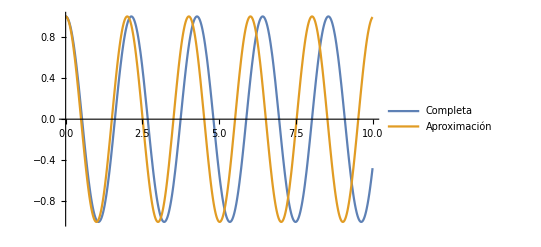

```mathematica
Plot[Evaluate[θ[t]/.{First[completa],First[aproximacion]}], {t,0,10},PlotLegends->{"Completa","Aproximación"}]
```

#### Ejercicio 1:

¿Cómo se comparar ambas soluciones en el espacio fase? Graficar.

#### Ejercicio 2:

El modelo de Lotka-Volterra consiste en una descripción de la ecología de un sistema donde existen presas y depredadores. Las ecuaciones que describen la dinámica son

-Graphics-

lo cual nos dice que el sistema está acoplado. x es la cantidad de presas, y la cantidad de depredadores. α, β, γ, δ son parámetros que describen la interacción entre ambas especies. El ejercicio consiste en modelar este sistema y graficar la cantidad de presas y depredadores en el tiempo. Los parámetros de interacción se pueden fijar de antemano a valores arbitrarios o se pueden hacer variar por medio de un Manipulate.

#### Ejercicio 3:

Tratemos de predecir la población máxima que puede haber en Mexico. Mathematica posee bases de datos integradas que contienen información útil acerca de datos geográficos. Un ejemplo de esto es la información disponible en la función CountryData. Veamos por ejemplo la población en Mexico entre los añis 1900 y 2018.

```mathematica
poblacionEnAños = CountryData["Mexico",{{"Population"},{1900,2018}}]
```

TimeSeries[…]

Mathematica nos devuelve una serie de tiempo, que es un objeto que representa toda esta información. Podemos acceder a los datos que contiene la serie de tiempo utilizando la función Normal[].

```mathematica
normalizado = Normal[poblacionEnAños];
```

```mathematica
normalizado[[1;;10]]
```

{{Mon 1 Jan 1900 00:00:00GMT-5.,13607000 people},{Tue 1 Jan 1901 00:00:00GMT-5.,13755000 people},{Wed 1 Jan 1902 00:00:00GMT-5.,13905000 people},{Thu 1 Jan 1903 00:00:00GMT-5.,14056000 people},{Fri 1 Jan 1904 00:00:00GMT-5.,14209000 people},{Sun 1 Jan 1905 00:00:00GMT-5.,14363000 people},{Mon 1 Jan 1906 00:00:00GMT-5.,14519000 people},{Tue 1 Jan 1907 00:00:00GMT-5.,14677000 people},{Wed 1 Jan 1908 00:00:00GMT-5.,14837000 people},{Fri 1 Jan 1909 00:00:00GMT-5.,14998000 people}}

La manera en la que Mathematica nos devuelve estos datos es en forma de objetos simbólicos que contienen unidades. Podemos procesarlos un poco más para obtener magnitudes numéricas. Se comenzará con la convención de que el primer año será 1900.

```mathematica
datos = Map[{DateValue[First[#],"Year"]-1900,QuantityMagnitude[Last[#]]}&,normalizado]
```

{{0,13607000},{1,13755000},{2,13905000},{3,14056000},{4,14209000},{5,14363000},{6,14519000},{7,14677000},{8,14837000},{9,14998000},{10,15160000},{11,15083000},{12,15007000},{13,14931000},{14,14855000},{15,14780000},{16,14705000},{17,14630000},{18,14556000},{19,14482000},{20,14409000},{21,14335000},{22,14566000},{23,14801000},{24,15040000},{25,15282000},{26,15528000},{27,15778000},{28,16032000},{29,16290000},{30,16553000},{31,16840000},{32,17132000},{33,17429000},{34,17731000},{35,18038000},{36,18350000},{37,18668000},{38,18991000},{39,19320000},{40,19815000},{41,20332000},{42,20866000},{43,21418000},{44,21988000},{45,22576000},{46,23183000},{47,23811000},{48,24461000},{49,25132000},{50,26282000},{51,27039000},{52,27846000},{53,28701000},{54,29605000},{55,30557000},{56,31557000},{57,32607000},{58,33704000},{59,34851000},{60,34994000},{61,36158000},{62,37367000},{63,38623000},{64,39928000},{65,41284000},{66,42694000},{67,44161000},{68,45686000},{69,47274000},{70,51868335},{71,53441943},{72,55081201},{73,56771626},{74,58492118},{75,60224601},{76,61969362},{77,63723359},{78,65461471},{79,67152555},{80,68776411},{81,70318386},{82,71788766},{83,73223336},{84,74673296},{85,76175154},{86,77741110},{87,79358780},{88,81010093},{89,82666457},{90,84306602},{91,85923799},{92,87523328},{93,89109703},{94,90691331},{95,92272749},{96,93858373},{97,95441345},{98,97001933},{99,98513690},{100,99959594},{101,101329543},{102,102634153},{103,103902569},{104,105175967},{105,106483757},{106,107835259},{107,109220753},{108,110627158},{109,112033369},{110,113423047},{111,114793341},{112,116146768},{113,117478371},{114,118783265}}

La gráfica de estos datos parece indicar un crecimiento del tipo logístico.

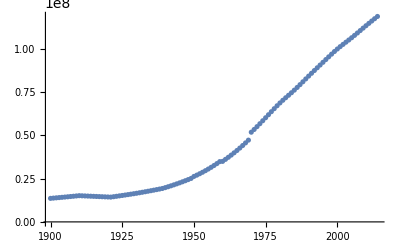

```mathematica
ListPlot[datos]
```

Dado que la ecuación que describe el crecimiento logístico es

-Graphics-

donde r es la tasa de crecimiento y K la capacidad de carga, encontrar la capacidad de carga de Mexico.

Pasos:
1- Resolver la ecuación diferencial con DSolve
2- Ajustar los datos usando FindFit. Nota: Será necesario aplicar constricciones a los valores de r y K.

#### Solución:

```mathematica
P0 = 13607000;
```

```mathematica
DSolve[{P'[t] == r P[t](1-P[t]/k),P[0] == P0},P,t]//Quiet
```

{{P→Function[{t},(13607000 ⅇ^(r t) k)/(-13607000+13607000 ⅇ^(r t)+k)]}}

fit =FindFit[datos,{(k P0 Exp[r t])/(k+P0 (Exp[r t]-1)),{k>0,r>0}},{k,r},t]

```mathematica
Plot[Evaluate[(k P0 Exp[r t])/(k+P0 (Exp[r t]-1)) /. fit],{t,0,1000}]
```

Sistema acoplado: Péndulo doble

-Graphics-

-Graphics-
-Graphics-
-Graphics-
-Graphics-

### Ejercicio 1:

A partir de este sistema de ecuaciones, resolver numéricamente y graficar la dinámica y el espacio fase.

#### Solución:

```mathematica
tMax =300;
With[
{
m1=10.0,m2=5,
l=20.0,g=9.81
},
(* Solución numérica *)sol = NDSolve[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == 1, θ2[0] == 0, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->40
]
];

(* Gráficas *)
SetOptions[{Plot,ParametricPlot,ParametricPlot3D},BaseStyle->{FontSize->13}];
Plot[Evaluate[θ1[t]/.sol],{t,0,tMax},PlotRange->All,AxesLabel->{Style["t", 15], Style["θ1(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15]]
Plot[Evaluate[θ2[t]/.sol],{t,0,tMax},PlotRange->All,AxesLabel->{Style["t", 15], Style["θ2(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15]]
ParametricPlot[Evaluate[{θ1[t],θ2[t]}/.sol],{t,0,tMax},AxesLabel->{Style["θ1(t)", 15], Style["θ2(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo θ1(t) vs θ2(t)", 15]]
ParametricPlot[Evaluate[{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.sol],{t,0,tMax},AxesLabel->{Style["X", 15], Style["Y", 15]},PlotLabel->Style["Trayectoria", 15], GridLines->Automatic]

ParametricPlot3D[{Evaluate[{θ1[t],θ1'[t], θ1''[t]}/.sol],Evaluate[{θ2[t],θ2'[t], θ2''[t]}/.sol]},{t,0,0.6*tMax},PlotRange->All,AxesLabel->{Style["θ(t)", 15], Style["θ'(t)", 15],Style["θ''(t)", 15]},PlotLabel->Style["Órbitas", 15],
PlotLegends->SwatchLegend[{"Masa 1","Masa 2"}, LegendFunction->"Frame"]
]
```

### Ejercicio 2:

Crear visualización del sistema utilizando primitivas gráficas. Para esto será necesario pasar del sistema de coordenadas de los péndulos al sistema cartesiano. Pueden hacer esto con las funciones:

```mathematica
Mass1Position[t_,solution_]:=Block[{θ1},{Sin[θ1[t]],-Cos[θ1[t]]}/.First[solution]];
Mass2Position[t_,solution_]:=Block[{θ1,θ2},{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.First[solution]];
```

que aceptan como argumentos el tiempo y la solución numérica dada por una función de interpolación.

#### Solución:

```mathematica
Mass1Position[t_,solution_]:=Block[{θ1},{Sin[θ1[t]],-Cos[θ1[t]]}/.First[solution]];
Mass2Position[t_,solution_]:=Block[{θ1,θ2},{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.First[solution]];
DynamicModule[{plt1,plt2},
Manipulate[
plt1 = ParametricPlot[Mass2Position[t,sol],{t,0,tm},Axes->False,PlotRange->{{-2,2},{-2,0}},ImageSize->500,PerformanceGoal->"Quality"];
plt2 = Graphics[
{
Thick,Line[{{0,0},Mass1Position[tm,sol]}],
Thick,Line[{Mass1Position[tm,sol],Mass2Position[tm,sol]}],
EdgeForm[Thick],Red,Disk[Mass1Position[tm,sol],0.15],
EdgeForm[Thick],ColorData["WebSafe"]["#3399FF"],Disk[Mass2Position[tm,sol],0.15],
Black,Text["m_1",Mass1Position[tm,sol]],
Black,Text["m_2",Mass2Position[tm,sol]]
},
PlotRange->{{-2,2},{-2,0}},
ImageSize->500
];
Show[{plt1,plt2}]
,
{{tm,0.01,"Tiempo"},0.01,200,AnimationRate->3,Appearance->"Open"},
TrackedSymbols:>{tm}
]
]
```

Problema de los 3 cuerpos

-Graphics-

#### Ejercicio

Solucionar numéricamente el problema de los 3 cuerpos. Comenzar con las condiciones iniciales

```mathematica
{x1init,y1init}={0.7,-0.5};
{x2init,y2init}={-0.7,2};
{x3init,y3init}={0,0};

{vx1init,vy1init}={0.93240737/2,0.86473146/2};
{vx2init,vy2init}={0.93240737/2,0.86473146/2};
{vx3init,vy3init}={-0.93240737,-0.86473146};
m1 = m2 = m3 = 1;
```

#### Solución

```mathematica
dinamica = Block[
{
x1init,y1init,x2init,y2init,x3init,y3init,
vx1init,vy1init,vx2init,vy2init,vx3init,vy3init,
m1,m2,m3
},

{x1init,y1init}={0.7,-0.5};
{x2init,y2init}={-0.7,2};
{x3init,y3init}={0,0};

{vx1init,vy1init}={0.93240737/2,0.86473146/2};
{vx2init,vy2init}={0.93240737/2,0.86473146/2};
{vx3init,vy3init}={-0.93240737,-0.86473146};
m1 = m2 = m3 = 1;

NDSolve[
{
x1'[t]==vx1[t],y1'[t]==vy1[t],
x2'[t]==vx2[t],y2'[t]==vy2[t],
x3'[t]==vx3[t],y3'[t]==vy3[t],
 vx1'[t]==-(m2(x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),vy1'[t]==-(m2(y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),vx2'[t]==(m1(x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vy2'[t]==(m1 (y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vx3'[t]==(m1 (x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+(m2 (x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vy3'[t]==(m1 (y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+(m2 (y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),
x1[0]==x1init,y1[0]==y1init,x2[0]==x2init,y2[0]==y2init,x3[0]==x3init,y3[0]==y3init,
vx1[0]==vx1init,vy1[0]==vy1init,vx2[0]==vx2init,vy2[0]==vy2init,vx3[0]==vx3init,vy3[0]==vy3init
},
{x1,x2,x3,y1,y2,y3,vx1,vx2,vx3,vy1,vy2,vy3},
{t,0,20}
]
];
```

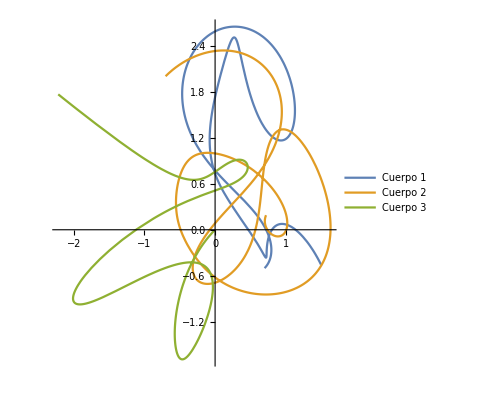

```mathematica
ParametricPlot[
Evaluate[{{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}}/. dinamica[[1]]],{t,0,20},
PlotLegends->{"Cuerpo 1", "Cuerpo 2","Cuerpo 3"}
]
```

#### Técnicas para hacerlo interactivo

Una forma de hacerlo interactivo es combinar la funcionalidad de primitivas gráficas y variables dinámicas.

```mathematica
DynamicModule[{xy0 = {0,0}, vxy0 = {1,1}},
Graphics[
{
Dashed,RGBColor[.2,.6,1],Dynamic[Arrow[{xy0,xy0+vxy0}]],
Locator[Dynamic[xy0+vxy0,(vxy0=#-xy0)&],Graphics[{Point[{0,0}]},ImageSize->10]],
Locator[Dynamic[xy0]]
},
PlotRange->{{-2,2},{-2,2}}
]
]
```

Esto se puede usar dentro de un Manipulate

```mathematica
PlotLocator[Dynamic[xy0_],Dynamic[vxy0_]]:=Graphics[
{
Dashed,RGBColor[.2,.6,1],Dynamic[Arrow[{xy0,xy0+vxy0}]],
Locator[Dynamic[xy0+vxy0,(vxy0=#-xy0)&],Graphics[{Point[{0,0}]},ImageSize->10]],
Locator[Dynamic[xy0]]
},
PlotRange->{{-2,2},{-2,2}}
];

Manipulate[
PlotLocator[Dynamic[xy0],Dynamic[vxy0]]
,
{{vxy0,{-0.5,-0.5}},{-2,-2},{2,2},ControlType->None},
{{xy0,{0.5,0.5}},{-2,-2},{2,2},ControlType->None}
,
SaveDefinitions->True
]
```

Este es un ejemplo del problema de los 3 cuerpos dentro de un módulo interactivo que permite cambiar la posición y velocidad inicial de uno de los cuerpos.

```mathematica
ThreeBody[{Dynamic[xy1init_],Dynamic[xy2init_],Dynamic[xy3init_]},{Dynamic[vxy1init_],Dynamic[vxy2init_],Dynamic[vxy3init_]}]:=Block[
{
x1init,y1init,x2init,y2init,x3init,y3init,
vx1init,vy1init,vx2init,vy2init,vx3init,vy3init,
m1,m2,m3,
dinamica
},

{x1init,y1init}=xy1init;
{x2init,y2init}=xy2init;
{x3init,y3init}=xy3init;

{vx1init,vy1init}=vxy1init;
{vx2init,vy2init}=vxy2init;
{vx3init,vy3init}=vxy3init;
m1 = m2 = m3 = 1;

dinamica = NDSolve[
{
x1'[t]==vx1[t],y1'[t]==vy1[t],
x2'[t]==vx2[t],y2'[t]==vy2[t],
x3'[t]==vx3[t],y3'[t]==vy3[t],
 vx1'[t]==-(m2(x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),vy1'[t]==-(m2(y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),vx2'[t]==(m1(x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vy2'[t]==(m1 (y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vx3'[t]==(m1 (x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+(m2 (x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vy3'[t]==(m1 (y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+(m2 (y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),
x1[0]==x1init,y1[0]==y1init,x2[0]==x2init,y2[0]==y2init,x3[0]==x3init,y3[0]==y3init,
vx1[0]==vx1init,vy1[0]==vy1init,vx2[0]==vx2init,vy2[0]==vy2init,vx3[0]==vx3init,vy3[0]==vy3init
},
{x1,x2,x3,y1,y2,y3,vx1,vx2,vx3,vy1,vy2,vy3},
{t,0,20}
];

Show[
ParametricPlot[
Evaluate[{{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}}/. dinamica[[1]]],{t,0,20},
PlotLegends->{"Cuerpo 1", "Cuerpo 2","Cuerpo 3"},
PlotRange->{{-4,4},{-4,4}}
],
Graphics[
{
Dashed,RGBColor[.2,.6,1],Dynamic[Arrow[{xy1init,xy1init+vxy1init}]],
Locator[Dynamic[xy1init+vxy1init,(vxy1init=#-xy1init)&],Graphics[{Point[{0,0}]},ImageSize->10]],
Locator[Dynamic[xy1init]]
},
PlotRange->{{-2,2},{-2,2}}
]
]
];

Manipulate[
ThreeBody[
{Dynamic[xy10],Dynamic[xy20],Dynamic[xy30]},{Dynamic[vxy10],Dynamic[vxy20],Dynamic[vxy30]}] 
,
{{vxy10,{0.93240737/2,0.86473146/2}},{-2,-2},{2,2},ControlType->None},
{{vxy20,{0.93240737/2,0.86473146/2}},{-2,-2},{2,2},ControlType->None},
{{vxy30,{-0.93240737,-0.86473146}},{-2,-2},{2,2},ControlType->None},
{{xy10,{ .7,-0.5}},{-2,-2},{2,2},ControlType->None},
{{xy20,{-0.7,2}},{-2,-2},{2,2},ControlType->None},
{{xy30,{0,0}},{-2,-2},{2,2},ControlType->None}
]
```

#### Ejercicio

Completar el módulo dinámico de manera que sea posible escoger las posiciones y velocidades iniciales de los tres cuerpos.

#### Solución

```mathematica
ThreeBody[{Dynamic[xy1init_],Dynamic[xy2init_],Dynamic[xy3init_]},{Dynamic[vxy1init_],Dynamic[vxy2init_],Dynamic[vxy3init_]}]:=Block[
{
x1init,y1init,x2init,y2init,x3init,y3init,
vx1init,vy1init,vx2init,vy2init,vx3init,vy3init,
m1,m2,m3,
dinamica
},

{x1init,y1init}=xy1init;
{x2init,y2init}=xy2init;
{x3init,y3init}=xy3init;

{vx1init,vy1init}=vxy1init;
{vx2init,vy2init}=vxy2init;
{vx3init,vy3init}=vxy3init;
m1 = m2 = m3 = 1;

dinamica = NDSolve[
{
x1'[t]==vx1[t],y1'[t]==vy1[t],
x2'[t]==vx2[t],y2'[t]==vy2[t],
x3'[t]==vx3[t],y3'[t]==vy3[t],
 vx1'[t]==-(m2(x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),vy1'[t]==-(m2(y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)),vx2'[t]==(m1(x1[t]-x2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vy2'[t]==(m1 (y1[t]-y2[t]))/(((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-(m3(y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vx3'[t]==(m1 (x1[t]-x3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+(m2 (x2[t]-x3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),vy3'[t]==(m1 (y1[t]-y3[t]))/(((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+(m2 (y2[t]-y3[t]))/(((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2)),
x1[0]==x1init,y1[0]==y1init,x2[0]==x2init,y2[0]==y2init,x3[0]==x3init,y3[0]==y3init,
vx1[0]==vx1init,vy1[0]==vy1init,vx2[0]==vx2init,vy2[0]==vy2init,vx3[0]==vx3init,vy3[0]==vy3init
},
{x1,x2,x3,y1,y2,y3,vx1,vx2,vx3,vy1,vy2,vy3},
{t,0,20}
];

Show[
ParametricPlot[
Evaluate[{{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}}/. dinamica[[1]]],{t,0,20},
PlotLegends->{"Cuerpo 1", "Cuerpo 2","Cuerpo 3"},
PlotRange->{{-4,4},{-4,4}}
],
Graphics[
{
Dashed,Dynamic[Arrow[{xy1init,xy1init+vxy1init}]],
Locator[Dynamic[xy1init+vxy1init,(vxy1init=#-xy1init)&],Graphics[{Point[{0,0}]},ImageSize->10]],
Locator[Dynamic[xy1init]]
,
Dashed,Dynamic[Arrow[{xy2init,xy2init+vxy2init}]],
Locator[Dynamic[xy2init+vxy2init,(vxy2init=#-xy2init)&],Graphics[{Point[{0,0}]},ImageSize->10]],
Locator[Dynamic[xy2init]]
,
Dashed,Dynamic[Arrow[{xy3init,xy3init+vxy3init}]],
Locator[Dynamic[xy3init+vxy3init,(vxy3init=#-xy3init)&],Graphics[{Point[{0,0}]},ImageSize->10]],
Locator[Dynamic[xy3init]]
},
PlotRange->{{-2,2},{-2,2}}
]
]
];

Manipulate[
ThreeBody[
{Dynamic[xy10],Dynamic[xy20],Dynamic[xy30]},{Dynamic[vxy10],Dynamic[vxy20],Dynamic[vxy30]}] 
,
{{vxy10,{0.93240737/2,0.86473146/2}},{-2,-2},{2,2},ControlType->None},
{{vxy20,{0.93240737/2,0.86473146/2}},{-2,-2},{2,2},ControlType->None},
{{vxy30,{-0.93240737,-0.86473146}},{-2,-2},{2,2},ControlType->None},
{{xy10,{ .7,-0.5}},{-2,-2},{2,2},ControlType->None},
{{xy20,{-0.7,2}},{-2,-2},{2,2},ControlType->None},
{{xy30,{0,0}},{-2,-2},{2,2},ControlType->None},
SaveDefinitions->True
]
```

¿Cómo saber si esta cosa es estable?
-Graphics-

Una herramiento para analizar el tipo de dinámica que se presenta en un sistema es la sección de Poincaré.

Simulación de galaxia

```mathematica
Mb = 1293;
b = 1.52;
Md = 2155;
a = b/0.2;
ah = 22.25;
ρ = 0.258;
G = 1;

axClassic[x_,y_,z_]:= -(G Mb x)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md x)/((x^2+y^2+z^2+a^2)^(3/2));
ayClassic[x_,y_,z_]:= -(G Mb y)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md y)/((x^2+y^2+z^2+a^2)^(3/2));
azClassic[x_,y_,z_]:= -(G Mb z)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md z)/((x^2+y^2+z^2+a^2)^(3/2));
ax[x_,y_,z_]:= -(G Mb x)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md x)/((x^2+y^2+z^2+a^2)^(3/2))+4 π G ρ ah^2 (x/((x^2+y^2+z^2)(1+(√(x^2+y^2+z^2))/ah))-(ah x Log[1+(√(x^2+y^2+z^2))/ah])/((x^2+y^2+z^2)^(3/2)));
ay[x_,y_,z_]:= -(G Mb y)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md y)/((x^2+y^2+z^2+a^2)^(3/2))+4 π G ρ ah^2 (y/((x^2+y^2+z^2)(1+(√(x^2+y^2+z^2))/ah))-(ah y Log[1+(√(x^2+y^2+z^2))/ah])/((x^2+y^2+z^2)^(3/2)));
az[x_,y_,z_]:= -(G Mb z)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md z)/((x^2+y^2+z^2+a^2)^(3/2))+4 π G ρ ah^2 (z/((x^2+y^2+z^2)(1+(√(x^2+y^2+z^2))/ah))-(ah z Log[1+(√(x^2+y^2+z^2))/ah])/((x^2+y^2+z^2)^(3/2)));


VBulge[r_]:= √((G Mb r^2)/((r^2+b^2)^(3/2)));
VDisk[r_]:= √((G Md r^2)/((r^2+a^2)^(3/2)));
VHalo[r_]:= √(4 π G ρ ah^3 Abs[1/(ah(1+r/ah))-Log[1+r/ah]/r]);
VTotal[r_]:=√(VBulge[r]^2+VDisk[r]^2+VHalo[r]^2);
```

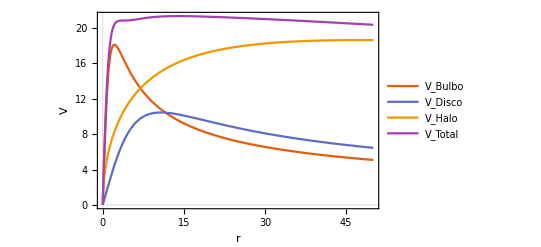

```mathematica
Plot[{VBulge[r],VDisk[r],VHalo[r],VTotal[r]},{r,0,50},PlotTheme->"Scientific",FrameLabel->{"r","V"},PlotLegends->{"V_Bulbo","V_Disco","V_Halo","V_Total"}]
```

```mathematica
Graphics3D[{Ellipsoid[{0,0,0},10*{1.5,1.5,1.2}],Ellipsoid[{0,0,0},10*{4,4,0.5}]}]
```

-Graphics3D-

```mathematica
CreatePoints[n_]:=Block[{pointsBulk,pointsHalo},
pointsBulk = RandomPoint[Ellipsoid[{0,0,0},10*{1.5,1.5,1.2}],n];
pointsHalo = RandomPoint[Ellipsoid[{0,0,0},10*{4,4,0.5}],Floor[n/2]];
Join[pointsBulk,pointsHalo]
];

CalculateOrbitWithoutDarkMatter[{x0_,y0_,z0_},{vx0_,vy0_,vz0_},tMax_ :100]:=Block[{x,y,z},
First@NDSolve[
{
x''[t] == axClassic[x[t],y[t],z[t]],
y''[t] == ayClassic[x[t],y[t],z[t]],
z''[t] == azClassic[x[t],y[t],z[t]],
x[0] == x0,x'[0] == vx0,y[0] == y0,y'[0]==vy0,z[0] == z0,z'[0]==vz0
},
{x,y,z},
{t,0,tMax}
]
];
CalculateOrbit[{x0_,y0_,z0_},{vx0_,vy0_,vz0_},tMax_ :100]:=Block[{x,y,z},
First@NDSolve[
{
x''[t] == ax[x[t],y[t],z[t]],
y''[t] == ay[x[t],y[t],z[t]],
z''[t] == az[x[t],y[t],z[t]],
x[0] == x0,x'[0] == vx0,y[0] == y0,y'[0]==vy0,z[0] == z0,z'[0]==vz0
},
{x,y,z},
{t,0,tMax}
]
];
CalculateInitialVelocity[{x_,y_,z_}]:={y/(√(x^2+y^2)),-x/(√(x^2+y^2)),0};
```

```mathematica
simulatedOrbit = ProgressMap[CalculateOrbitWithoutDarkMatter[#,25*CalculateInitialVelocity[#]]&,CreatePoints[5000]];
```

```mathematica
Manipulate[
ListPointPlot3D[
Evaluate[{x[t],y[t],z[t]}/.simulatedOrbit],
PlotRange->{{-60,60},{-60,60},{-60,60}},
PlotStyle->{White,PointSize[Small]},
Background->Black,
ImageSize->600
],
{t,0,10}
]
```

```mathematica
ExportName[file_,i_,total_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[total]];
directory = DirectoryName[file];
name = FileBaseName[file];
FileNameJoin[{directory,StringJoin[name,IntegerString[i,10,indexLength],".png"]}]
];
```

```mathematica
GalaxyPlot[simulatedOrbit_,t_]:=ListPointPlot3D[
Evaluate[{x[t],y[t],z[t]}/.simulatedOrbit],
PlotRange->{{-60,60},{-60,60},{-60,60}},
PlotStyle->{White,PointSize[Small]},
Background->Black,
ImageSize->600
];
```

```mathematica
ProgressTable[
Export[
ExportName[FileNameJoin[{NotebookDirectory[],"img","image.png"}],Floor[t/0.01],Floor[10/0.01]],
GalaxyPlot[simulatedOrbit,t]
],
{t,0,10,0.01}
];
```

$Aborted

Sección de Poincaré

### Del oscilador armónico simple

Supongamos que tenemos un oscilador armónico

(d^2 x(t))/dt^2 = - k x(t)

-Graphics-

Su órbita (gráfica de la posición) es

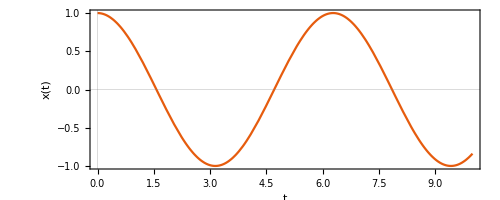

```mathematica
sol=NDSolve[
{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,{t,0,10}
][[1,1]];

ParametricPlot[Evaluate[{t,x[t]}/.sol],{t,0,10},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t","x(t)"}]
```

El estado del sistema en cualquier instante está determinado por un punto en el espacio fase.

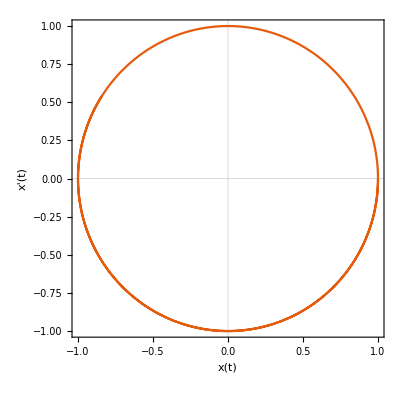

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.sol],{t,0,10},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"}]
```

Ahora, la pregunta es, ¿son necesarios todos los puntos de espacio fase para dar una descripción completa de la dinámica del sistema? Podemos notar que la órbita es periódica con periodo 2π, de manera que tomando el punto del espacio fase que ocurre cada intervalo de tiempo 2π tendremos una descripción del sistema a partir de la cual podemos reconstruir toda la dinámica, es decir, no se pierde información.

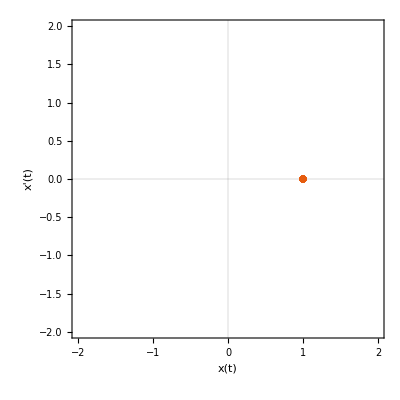

```mathematica
data=Reap[
NDSolve[
{x''[t]+x[t]==0,x[0]==1,x'[0]==0,WhenEvent[Mod[t,2π]==0,Sow[{x[t],x'[t]}]]},
x,
{t,0,100},
MaxSteps->∞
]
][[2,1]];
ListPlot[data,AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"},PlotRange->{{-2,2},{-2,2}}]
```

#### Ejercicio

Obtener la sección de Poincaré y la gráfica de un oscilador armónico forzado por una fuerza externa f_e = Cos(0.4 t). El plano de corte  lo pueden escoger de forma arbitraria, se recomienda crear un módulo dinámico que permita escoger una frecuencia arbitraria.

#### Solución

```mathematica
DynamicModule[{sol},
Manipulate[
sol=Reap[
NDSolve[
{x''[t]+x[t]==Cos[ 0.4t],x[0]==1,x'[0]==0,WhenEvent[Mod[t,f]==0,Sow[{x[t],x'[t]}]]},x,{t,0,1000},MaxSteps->∞
]
];
Column[
{
ParametricPlot[Evaluate[{t,x[t]}/.sol[[1]]],{t,0,30},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t","x'(t)"},ImageSize->500]
,
ListPlot[sol[[2,1]],AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"},PlotRange->{{-2,2},{-2,2}},PlotStyle->PointSize[Medium],ImageSize->500]
}
]
,
{{f,0.5},0.1,2 π}
]
]
```

### Del oscilador de Duffing

En ejemplo con una dinámica mucho más interesante es el oscilador de Duffing que físicamente puede representar un tipo de oscilador excitado bajo el amortiguamiento de un campo magnético. Este tipo de oscilador se presenta también en algunos sistemas electrónicos. Independientemente de su forma física la estructura matemática que describe su dinámica es una ecuación diferencial no lineal
-Graphics-

x^(..)(t) + δ ẋ(t) + α x(t) + β (x(t))^3 = γ Cos (ω t)

Esta ecuación no tiene solución analítica, y en su órbita presenta una dinámica muy compleja.

-Graphics-
-Graphics-

#### Ejercicio

Obtener la órbita en el espacio fase y la sección de Poincaré del oscilador de Duffing. ¿Qué nos dice de su dinámica?

### 3 cuerpos revisited

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

#### Ejercicio

A continuación se muestra una implementación de la dinámica del problema de 3 cuerpos restringido.

```mathematica
Manipulate[
threeBodyTrajectories[{Dynamic[vxy0],Dynamic[xy0]},vxy0,μ, T,ImageSize->{350,350}] 
,
{{T,20,"Tiempo"},10, 1000},
{{μ,1},0.01,10},
{{vxy0,{-0.5,-0.5}},{-2,-2},{2,2},ControlType->None},
{{xy0,{0.5,0.5}},{-2,-2},{2,2},ControlType->None},
ControlPlacement->{Top,Top,Top,Top,Top,Left,Left,Left},
Initialization:>(
threeBodyTrajectories[{Dynamic[vxy0_], Dynamic[xy0_]},
{vx0_,vy0_},μ_,T_,
plotOptions___] := 
Module[{nds,Tmax,prolog,funsToPlot,x0,y0},
{x0,y0}=xy0;
nds=NDSolve[
{x'[t]==vx[t],
y'[t]==vy[t],
vx'[t]==2 vy[t]+x[t]-((1-μ) (x[t]+μ))/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ (x[t]-1+μ))/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),
vy'[t]==-2 vx[t]+y[t]-((1-μ) y[t])/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ y[t])/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),

x[0]==x0,y[0]==y0,
vx[0]==vx0,vy[0]==vy0},
{x,y,vx,vy},{t,0,T}] // Quiet;

funsToPlot={x[t],y[t]}/. nds[[1]];
prolog = {PointSize[0.03],Transpose[{{RGBColor[1,.2,0],RGBColor[.5,.8,0]},{Point[{-0.5,0}],Point[{0.5,0}]}}]};
Show[ParametricPlot[Evaluate[funsToPlot],{t,0,T},
Prolog->prolog,
PlotStyle->{RGBColor[1,.2,0],RGBColor[.5,.8,0],RGBColor[.2,.6,1]},PlotRange->{{-2,2},{-2,2}},AspectRatio -> 1, MaxRecursion->ControlActive[3,9],plotOptions,PlotTheme->"Scientific", FrameLabel->{"x","y"},PlotLabel->"Órbita"],Graphics[{Dashed,RGBColor[.2,.6,1],Dynamic[Arrow[{xy0,xy0+vxy0}]],Locator[Dynamic[xy0+vxy0,(vxy0=#-xy0)&],Graphics[{Point[{0,0}]},ImageSize->10]],Locator[Dynamic[xy0]]}]]
];
)]
```

Obtener la sección de Poincaré en un módulo dinámico que la muestre junto con la trayectoria.

## Álgebra lineal

Transformaciones lineales

Sea una base conformada por los vectores  î= (a
c)  y  ĵ =  (b
d), y sea un vector v⃗ = (x
y) definido en la base î, ĵ.

La posición del vector v⃗  está dada por

v⃗  = x î + y  ĵ = x (a
c) + y (b
d) .

Si la base î, ĵ cambia, entonces la posición de v⃗ también cambiará. Podemos monitorear el cambio de v⃗ en función de la base utilizando un Manipulate.

```mathematica
PatternGrid[m_,n_]:=Map[
{{m.{-10,#},m.{10,#}},{m.{#,-10},m.{#,10}}}&,Range[-10,10,2/n]];
Lines[m_,n_]:=Map[Line,PatternGrid[m,n]];
```

```mathematica
DynamicModule[{m,lineas,eje,vector,etiquetas},
Manipulate[
m = Transpose[{i,j}];
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
etiquetas = {
Text[Panel[Style["î",14],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",14],FrameMargins->0],m.{0,0.5}],
Text[Panel[Style["v⃗",14],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.v]
};
vector = {Thick,Green,Arrow[{{0,0},m.v}]};
Column[
{
Style["Matriz",Bold],
MatrixForm[m],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,vector,etiquetas],PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->300]
},
Left,
1
]
,
{{i,{1,0}},Locator},
{{j,{0,1}},Locator},
{{v,{0.7,0.7}},{-1,-1},{1,1}},
SaveDefinitions->True
]
]
```

Es notable que v⃗  = x î + y  ĵ = x (a
c) + y (b
d)  es en esencia una transformación lineal definida por

(a | b
c | d) (x
y) = (ax + by
cx + dy),

esto implica que una transformación lineal se puede visualizar como una transformación del espacio. En Mathematica las operaciones entre matrices se pueden hacer con el operador Dot, por ejemplo:

```mathematica
m = ({{a, b}, {c, d}}); v = ({{x}, {y}});
m.v
```

```mathematica
FullForm[Hold[m.v]]
```

Y evalúa a lo que se espera obtener de una transformación lineal.

```mathematica
MatrixForm[m.v]
```

### Ejercicios

#### Ejercicio 1:

Resolver el sistema de ecuaciones

-Graphics-

utilizando matrices. La matriz inversa se puede encontrar con la función Inverse[].

#### Ejercicio 2:

Crear una visualización de una matriz de rotación. El parámetro en el Manipulate será un ángulo θ, y se transformará un vector arbitrario. Visualizar el vector original y el transformado.

Determinante

La determinante se puede interpretar como la magnitud de cambio de área de una figura a causa de un cambio en la base.

```mathematica
image =ImageResize[ExampleData[{"TestImage","Flower"}],300];
figure = Map[Dot[({{0.5, 0}, {0, 0.5}}),#]+{0.5,0.5}&,CirclePoints[6]];
DynamicModule[{m,lineas,eje,polygon,etiquetas},
Manipulate[
m = Transpose[{i,j}];
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
polygon = {Texture[image],Polygon[Map[Dot[m,#]&,figure],VertexTextureCoordinates->CirclePoints[6]]};
etiquetas = {
Text[Panel[Style["î",14],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",14],FrameMargins->0],m.{0,0.5}]
};

Column[
{
Style["Matriz",Bold],
MatrixForm[m],
Style["Determinante",Bold],
Det[m],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,polygon,etiquetas],PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->300]
},
Left,
1
]
,
{{i,{1,0}},Locator},
{{j,{0,1}},Locator},
SaveDefinitions->True
]
]
```

Se puede calcular la determinante con la función Det[]

```mathematica
Det[({{a, b}, {c, d}})]
```

### Ejercicio:

Resolver el mismo sistema de ecuaciones
-Graphics-
utilizando determinantes.

Eigenvectores

Un eigenvector debe cumplir la propiedad de que

A v = λ v

¿Cómo se puede visualizar esto?

#### Solución:

```mathematica
Clear[v];
DynamicModule[{m,mEigenvectores,mEigenvalores,lineas,eje,vector,span,eigenvectores,etiquetas,eigenEtiquetas},
Manipulate[
m = Transpose[{i,j}];
mEigenvectores = Eigenvectors[m];
mEigenvalores = Eigenvalues[m];
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
span = {Thick,Orange,Arrow[{{0,0},v}]};
vector = {Thick,Green,Arrow[{{0,0},m.v}]};
etiquetas = {
Text[Panel[Style["î",12],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",12],FrameMargins->0],m.{0,0.5}],
Text[Panel[Style["span",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).v],
Text[Panel[Style["v⃗",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.v]
};


If[!MemberQ[mEigenvalores,_Complex],
eigenvectores = {
Dashed,Purple,Arrow[{{0,0},First[mEigenvectores]}],
Dashed,Brown,Arrow[{{0,0},Last[mEigenvectores]}]
};
eigenEtiquetas = {
Text[Panel[Style["OverVector[v_1]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).First[mEigenvectores]],
Text[Panel[Style["OverVector[v_2]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.Last[mEigenvectores]]
};
,
eigenvectores = {};
eigenEtiquetas ={};
];

Column[
{
Style["Matriz",Bold],
MatrixForm[m],
Style["Eigenvalores",Bold],
mEigenvalores,
Style["Eigenvectores",Bold],
Row[Map[Row,Transpose[{{"v_1 = ","v_2 = "},Map[MatrixForm,mEigenvectores]}]],", "],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,vector,span,eigenvectores,etiquetas,eigenEtiquetas],PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->300]
},
Left,
1
]
,
{{i,{1,0}},Locator},
{{j,{0,1}},Locator},
{{v,{0.7,0.7}},Locator},
SaveDefinitions->True
]
]
```

Proyecto: Eigen-estados cuánticos de un potencial bidimensional

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

El objetivo del proyecto es implementar el método de expansión utilizando un potencial con una geometría complicada (triángulo, polígono, círculo cortado, etc.. )

El proyecto se dividirá en los siguietes pasos.

1. Primero es necesario establecer la base sobre la cual se construye el método de expansión. Para este proyecto será dada la base y la función para calcular los elementos de la matriz ν.

```mathematica
ϕm[x_,y_,a1_,a2_,{m1_,m2_}]:=√(2/a1) Sin[(π m1 x)/a1] √(2/a2) Sin[(π m2 y)/a2];
ν[k1_,k2_,a1_,a2_,base_,regionII_]:=Module[{},
Quiet[NIntegrate[ϕm[x,y,a1,a2,Part[base,k1]]  ϕm[x,y,a1,a2,Part[base,k2]],{x,y}∈regionII,Method->"MonteCarlo"]]
];

MSize = 5;
baseIndexes=Flatten[Table[{m1,m2},{m1,1,MSize},{m2,1,MSize}],1];
```

Nótese que la integral se realiza sobre una región definida como regionII. Comencemos entonces definiendo la región. Dada una regiónI, ¿cómo podemos definir la regiónII? Por simplicidad hagamos primero que

```mathematica
regionI = Disk[]
```

2. Ya tenemos la regiónII, ahora es necesario encontrar los valores de a1 y a2.  Podemos hacer uso de la siguiente función. ¿Qué es lo que hace? Explicar.

```mathematica
GetRegionDimensions[region_]:=Map[Abs[Apply[Subtract,#]]&,RegionBounds[region]];
```

3. Es la hora de hacer el cálculo más tardado del proyecto, construir la matriz νnm. Aquí son especialmente útiles los índices de la base.

4. Calcular δCoeff y δnm tal que se pueda construir la matriz del hamiltoniano dada por:

5. Obtener las energías En y los eigenvectores cm.

6. Por último, graficar la norma al cuadrado de la función de onda de cada eigenestado. Esto nos da la densidad de probabilidad de encontrar a la partícula en un punto determinado.

```mathematica
ψ[x_,y_,a1_,a2_,eigenstate_,base_,cm_]:=Sum[cm[[eigenstate,k]] ϕm[x,y,a1,a2,Part[base,k]],{k,1,Length[base]}];
```

```mathematica
Hnm = δCoeff*δnm + V0*νnm;
```

Un ejemplo del tipo de gráfica que se espera es el siguiente.

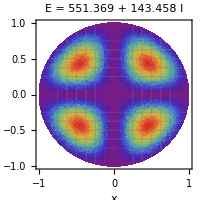

#### Solución

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
ϕm[x_,y_,a1_,a2_,{m1_,m2_}]:=√(2/a1) Sin[(π m1 x)/a1] √(2/a2) Sin[(π m2 y)/a2];
ν[k1_,k2_,a1_,a2_,base_,regionII_]:=Module[{},
Quiet[NIntegrate[ϕm[x,y,a1,a2,Part[base,k1]]  ϕm[x,y,a1,a2,Part[base,k2]],{x,y}∈regionII,Method->"MonteCarlo"]]
];
```

```mathematica
GetRegionDimensions[region_]:=Map[Abs[Apply[Subtract,#]]&,RegionBounds[region]];
CalculateEigenstates[regionI_,MSize_]:=Module[
{regionIBoundingBox,regionII,baseIndexes,νnm,δnm,δCoeff,Hnm,En,cm,a1,a2,ℏ = 1,m = 1,V0 = 200000,Δ = 0.000001},

regionIBoundingBox = Apply[Rectangle,Transpose[RegionBounds[regionI]]+{Δ,-Δ}];
regionII = RegionDifference[regionIBoundingBox,regionI];

baseIndexes=Flatten[Table[{m1,m2},{m1,1,MSize},{m2,1,MSize}],1];
{a1,a2} = GetRegionDimensions[regionI];
νnm = ProgressTable[ν[k1,k2,a1,a2,baseIndexes,regionII],{k1,1,Length[baseIndexes]},{k2,1,Length[baseIndexes]},"ShowInfo"->True];
δnm = IdentityMatrix[Length[baseIndexes]];

δCoeff = Table[(ℏ^2 π^2)/(2 m)Total[Part[baseIndexes,k]^2/{a1,a2}^2],{k,1,Length[baseIndexes]}];
Hnm = δCoeff*δnm + V0*νnm;
En = Sort[Eigenvalues[Hnm]];
cm = Part[Eigenvectors[Hnm],Ordering[Eigenvalues[Hnm]]];
Return[{a1,a2,baseIndexes,En,cm,Hnm}];
];
```

```mathematica
ψ[x_,y_,a1_,a2_,eigenstate_,base_,cm_]:=Sum[cm[[eigenstate,k]] ϕm[x,y,a1,a2,Part[base,k]],{k,1,Length[base]}];
```

```mathematica
regionI = Disk[];
{a1,a2,baseIndexes,En,cm,Hnm} = CalculateEigenstates[regionI,2];
```

$Aborted

```mathematica
Table[
DensityPlot[Abs[ψ[x,y,a1,a2,eigenstate,baseIndexes,cm]]^2,{x,y}∈regionI,
Axes->True,
FrameLabel->{"x", "y"},
AxesOrigin->{1,1},
ColorFunction->"Rainbow",
Mesh->Automatic,
ImageSize->200,
PerformanceGoal->"Quality",
PlotLabel->StringJoin["E = ",ToString[En[[eigenstate]]]],
PlotRange->All,
PlotPoints->35
]
,
{eigenstate,1,Length[base]}
]
```